```mathematica
(*{σ,Blue,Dashed,Thick},{ρ,Red,Dashed,Thick},{pi,Darker[Black],Thick,Dashed},{a1,Green,Dashed},{ψ,Purple}*)
```

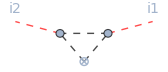

```mathematica
<<FormTracer`
```

FormTracer 2.3.6 loaded.

Copyright (C) 2013-2018, Anton K. Cyrol, Mario Mitter, Jan M. Pawlowski, and Nils Strodthoff.
FormTracer is released under the GNU General Public License version three or later.

If used in scientific publications, please acknowledge our work by citing:
A. K. Cyrol, M. Mitter, and N. Strodthoff, Comput. Phys. Commun. 219C (2017) 346-352, arXiv:1610.09331 [hep-ph]

Using FORM 4.0 (Apr 10 2012) 32-bits.

```mathematica
Unprotect[DiracDelta,Times,Integrate,Plus,Dot];
V[q_,d_]:=(2 π^(d/2))/Gamma[d/2]*momlor[q,1]^(d-1)
Integrate[HeavisideTheta[k_^2-x_^2]*y_,{x_,0,∞},res___]:=Integrate[Simplify[y,Assumptions->0<x<k],{x,0,k},res]
nf[-x_]:=1-nf[x]
nf[-Ek+μ]:=1-nf[Ek-μ]
nf'[-Ek+x___]:=nf'[Ek-x]
nf[-Ek+ⅈ p0+x_]:=1-nf[Ek-ⅈ p0-x]
nf[-Ek+ⅈ p0]:=1-nf[Ek-ⅈ p0]
nf[Ek+ⅈ p0+x___]:=nf[Ek+x]
nf[Ek-ⅈ p0+x___]:=nf[Ek+x]
nb[-x_]:=-(1+nb[x])
nb'[-x_]:=nb'[x]
nb'[-Ek-ⅈ p0]:=nb'[Ek+ⅈ p0]
nb'[Ek+ⅈ p0]:=nb'[Ek]
nb'[Ek-ⅈ p0]:=nb'[Ek]
nb[x_-ⅈ p0]:=nb[x]
nb[-Ek+ⅈ p0]:=-(1+nb[Ek-ⅈ*p0])
SetAttributes[CircleDot,{Orderless,Flat}]
(a_+b_)⊙c_:=a⊙c+b⊙c
a_⊙(num_?NumberQ b_):=num*a⊙b
p1⊙b_:=0
SetAttributes[Dot,{Orderless}]
q1.q1:=momlor[q1,0]^2+momlor[q1,1]^2
p1.q1:=momlor[p1,0]*momlor[q1,0]
p1.p1:=momlor[p1,0]^2+momlor[p1,1]^2
Dot[a_+b_,c_]:=a.c+b.c
Dot[a_,(num_?NumberQ b_)]:=num*a.b
momlor[a_+b_,c_]:=momlor[a,c]+momlor[b,c]
momlor[p1,1]:=0
```

```mathematica
DefineLorentzTensors[δ[μ,ν],momlor[p,μ],p.q,ϵ[],δS[i,j],γ[μ,i,j],γ5[i,j],momlors[p,μ],p⊙q]
AddExtraVars[m,k,mp,mf,g,hv,ms];
DefineFormAutoDeclareFunctions[{HeavisideTheta,Power,pR,prop,Z}];
DefineGroupTensors[{
{SU2fundexplicit(*group type*),{SU2f(*name of group*),2(*dimension of representation*)
(*(*more options for groups of type GenericGroup: *),cR(*quadratic casimir operator of representation*),NA(*dimension of adjoint representation*),cA(*quadratic casimir operator of adjoint representation*),I2R(*second order index of representation (normalisation)*)*)},
δA[a,b](*Kronecker delta in adjoint space*),f[a,b,c](*structure constants*),δF[i,j](*Kronecker delta in representation space*),τ[a,i,j](*generators of representation*)}
}];
```

```mathematica
Γffb[{i1_,i2_},{i_,j1_,j2_}]:=(*2ⅈ**)ⅈ*γ5[i1,i2](**τ[i,j1,j2]*)
fer[q1_,μ_,i_,j_]:=((-ⅈ(momlor[q1,μ]γ[μ,i,j]+rf*momlors[q1,μ]*γ[μ,i,j]))Zf[k]+mf*δS[i,j])/((momlor[q1,0]^2+(1+rf)^2*momlor[q1,1]^2)Zf[k]+mf^2)
piprop[q1_]:=1/((momlor[q1,0]^2+(1+rb)*momlor[q1,1]^2)Zphi[k]+mp^2)
sigprop[q1_]:=1/((momlor[q1,0]^2+(1+rb)*momlor[q1,1]^2)Zphi[k]+mp^2)
Rf[q1_,μ_,i_,j_]:=1/momlor[q1,1] ⅈ HeavisideTheta[k^2-momlor[q1,1]^2]momlors[q1,μ]γ[μ,i,j]
Rb[q1_]:=2 k HeavisideTheta[k^2-momlor[q1,1]^2];
rf=Simplify[(√(k^2/momlor[q1,1]^2)-1)*HeavisideTheta[k^2-momlor[q1,1]^2],Assumptions->k>0&&momlor[q1,1]>0];
rb=Simplify[(k^2/momlor[q1,1]^2-1)*HeavisideTheta[k^2-momlor[q1,1]^2],Assumptions->k>0&&momlor[q1,1]>0];
pipirho[p_,q_,a_,b_,c_,μ_]:=ⅈ*g*f[a,b,c]*(momlor[p,μ]-momlor[q,μ])
pipirhorho[i_,j_,k_,l_,μ_,ν_]:=g^2*(2*δA[i,j]δA[k,l]-δA[i,k]δA[j,l]-δA[i,l]δA[j,k])
pipirsigsig[i_,j_]:=2 g^2*δA[i,j]
pipira1a1[i_,j_,k_,l_]:=g^2(δA[i,k]δA[j,l]+δA[i,l]δA[j,k])
ferferrho[μ_,i_,j_]:=ⅈ*hv*γ[μ,i,j]
ferfera1[μ_,i_,j_]:=Module[{tij},ⅈ*hv*γ[μ,i,tij]γ5[tij,j]]
sigpia1[p_,q_,i_,j_,μ_]:=ⅈ*g*δA[i,j]*(momlor[p,μ]-momlor[q,μ])
```

```mathematica
loopexpr=FormTrace[Rb[q1+p1]*sigprop[q1+p1]sigpia1[q1+p1,-q1,i,j,μ]piprop[q1]sigpia1[-q1,p1+q1,j,i,μ]sigprop[q1+p1]];
test1=Simplify[Expand[Simplify[V[q1,3]*1/(2π)^3 loopexpr]/.q1⊙q1->momlor[q1,1]^2]];
```

```mathematica
loopfunctionint2=Integrate[test1,{momlor[q1,1],0,∞},GenerateConditions->False]
```

(g^2 k^4 (12 k^2+5 (momlor[p1,0]+2 momlor[q1,0])^2))/(5 π^2 (mp^2+(k^2+momlor[q1,0]^2) Zphi[k]) (mp^2+(k^2+(momlor[p1,0]+momlor[q1,0])^2) Zphi[k])^2)

```mathematica
loopfunctionint2=(g^2 k^4 (12 k^2+5 (momlor[p1,0]+2 momlor[q1,0])^2))/(5 π^2 (mp^2+(k^2+momlor[q1,0]^2) Zphi[k]) (s+(k^2+(momlor[p1,0]+momlor[q1,0])^2) Zphi[k]));
```

```mathematica
poles=TransferFunctionPoles[TransferFunctionModel[loopfunctionint2,momlor[q1,0]]][[1,1]]
```

{-(√(-mp^2-k^2 Zphi[k]))/(√Zphi[k]),(√(-mp^2-k^2 Zphi[k]))/(√Zphi[k]),(-momlor[p1,0] Zphi[k]-√(-s Zphi[k]-k^2 Zphi[k]^2))/Zphi[k],(-momlor[p1,0] Zphi[k]+√(-s Zphi[k]-k^2 Zphi[k]^2))/Zphi[k]}

```mathematica
1/3 FullSimplify[FullSimplify[(-D[Simplify[1/(2ⅈ)*Sum[(1+2nb[ⅈ*i])Residue[loopfunctionint2,{momlor[q1,0],i}],{i,poles}],Assumptions->k>0&&mp>0&&s>0&&Zphi[k]>0&&Zphi[k]>0&&Zf[k]>0]/.{√(k^2+mp^2)->Ek,n_. k^2+n_. mp^2->n*Ek^2,Zf[k]->1,Zphi[k]->1},s]/.s->mp^2)/.{√(k^2+mp^2)->Ek,n_. k^2+n_. mp^2->n*Ek^2,momlor[p1,0]->p0},Assumptions->Ek>0]//.{k^2->Ek^2-mp^2}]
```

(g^2 k^4 ((224 Ek^4-12 mp^2 p0^2+5 p0^4+Ek^2 (-144 mp^2+52 p0^2)) (1+2 nb[Ek])-2 Ek (4 Ek^2+p0^2) (32 Ek^2-12 mp^2+5 p0^2) nb'[Ek]))/(60 Ek^3 (4 Ek^2+p0^2)^2 π^2)

```mathematica
1/3(-D[Simplify[1/(2ⅈ)*Sum[(1+2nb[ⅈ*i])Residue[loopfunctionint2,{momlor[q1,0],i}],{i,poles}],Assumptions->k>0&&mp>0&&s>0&&Zphi[k]>0&&Zphi[k]>0&&Zf[k]>0]/.{√(k^2+mp^2)->Ek,n_. k^2+n_. mp^2->n*Ek^2},s]/.s->mp^2)
```

1/(60 π^2 Zphi[k]^(3/2))g^2 k^4 ((20 (1+2 nb[-ⅈ momlor[p1,0]-√(k^2+mp^2/Zphi[k])]) (1-(momlor[p1,0] Zphi[k])/(2 √(-Zphi[k] (mp^2+k^2 Zphi[k])))))/(√(mp^2+k^2 Zphi[k]) (-momlor[p1,0]^2 Zphi[k]+2 ⅈ momlor[p1,0] √(Zphi[k] (mp^2+k^2 Zphi[k]))))+(20 (1+2 nb[-ⅈ momlor[p1,0]+√(k^2+mp^2/Zphi[k])]) (1-(ⅈ momlor[p1,0] Zphi[k])/(2 √(Zphi[k] (mp^2+k^2 Zphi[k])))))/(√(mp^2+k^2 Zphi[k]) (momlor[p1,0]^2 Zphi[k]+2 ⅈ momlor[p1,0] √(Zphi[k] (mp^2+k^2 Zphi[k]))))-((1+2 nb[-ⅈ momlor[p1,0]-√(k^2+mp^2/Zphi[k])]) (1+(ⅈ momlor[p1,0] Zphi[k])/(√(Zphi[k] (mp^2+k^2 Zphi[k])))) ((8 k^2-5 momlor[p1,0]^2) Zphi[k]+20 (mp^2+momlor[p1,0] √(-Zphi[k] (mp^2+k^2 Zphi[k])))))/(√(mp^2+k^2 Zphi[k]) (-momlor[p1,0]^2 Zphi[k]+2 ⅈ momlor[p1,0] √(Zphi[k] (mp^2+k^2 Zphi[k])))^2)-((1+2 nb[-ⅈ momlor[p1,0]-√(k^2+mp^2/Zphi[k])]) ((8 k^2-5 momlor[p1,0]^2) Zphi[k]+20 (mp^2+momlor[p1,0] √(-Zphi[k] (mp^2+k^2 Zphi[k])))))/(2 (mp^2+k^2 Zphi[k])^(3/2) (-momlor[p1,0]^2 Zphi[k]+2 ⅈ momlor[p1,0] √(Zphi[k] (mp^2+k^2 Zphi[k]))))-((1+2 nb[√(k^2+mp^2/Zphi[k])]) ((8 k^2-5 momlor[p1,0]^2) Zphi[k]+20 (mp^2-ⅈ momlor[p1,0] √(Zphi[k] (mp^2+k^2 Zphi[k])))))/(√(mp^2+k^2 Zphi[k]) (momlor[p1,0]^2 Zphi[k]+2 ⅈ momlor[p1,0] √(Zphi[k] (mp^2+k^2 Zphi[k])))^2)-((1+2 nb[-ⅈ momlor[p1,0]+√(k^2+mp^2/Zphi[k])]) (-1+(ⅈ momlor[p1,0] Zphi[k])/(√(Zphi[k] (mp^2+k^2 Zphi[k])))) ((8 k^2-5 momlor[p1,0]^2) Zphi[k]+20 (mp^2-ⅈ momlor[p1,0] √(Zphi[k] (mp^2+k^2 Zphi[k])))))/(√(mp^2+k^2 Zphi[k]) (momlor[p1,0]^2 Zphi[k]+2 ⅈ momlor[p1,0] √(Zphi[k] (mp^2+k^2 Zphi[k])))^2)-((1+2 nb[-ⅈ momlor[p1,0]+√(k^2+mp^2/Zphi[k])]) ((8 k^2-5 momlor[p1,0]^2) Zphi[k]+20 (mp^2-ⅈ momlor[p1,0] √(Zphi[k] (mp^2+k^2 Zphi[k])))))/(2 (mp^2+k^2 Zphi[k])^(3/2) (momlor[p1,0]^2 Zphi[k]+2 ⅈ momlor[p1,0] √(Zphi[k] (mp^2+k^2 Zphi[k]))))-((1+2 nb[1/(√(Zphi[k]/(mp^2+k^2 Zphi[k])))]) ((8 k^2-5 momlor[p1,0]^2) Zphi[k]+20 (mp^2+ⅈ momlor[p1,0] √(Zphi[k] (mp^2+k^2 Zphi[k])))))/(√(mp^2+k^2 Zphi[k]) (-momlor[p1,0]^2 Zphi[k]+2 ⅈ momlor[p1,0] √(Zphi[k] (mp^2+k^2 Zphi[k])))^2)-(((8 k^2-5 momlor[p1,0]^2) Zphi[k]+20 (mp^2+momlor[p1,0] √(-Zphi[k] (mp^2+k^2 Zphi[k])))) nb'[-ⅈ momlor[p1,0]-√(k^2+mp^2/Zphi[k])])/(√(k^2+mp^2/Zphi[k]) Zphi[k] √(mp^2+k^2 Zphi[k]) (-momlor[p1,0]^2 Zphi[k]+2 ⅈ momlor[p1,0] √(Zphi[k] (mp^2+k^2 Zphi[k]))))+(((8 k^2-5 momlor[p1,0]^2) Zphi[k]+20 (mp^2-ⅈ momlor[p1,0] √(Zphi[k] (mp^2+k^2 Zphi[k])))) nb'[-ⅈ momlor[p1,0]+√(k^2+mp^2/Zphi[k])])/(√(k^2+mp^2/Zphi[k]) Zphi[k] √(mp^2+k^2 Zphi[k]) (momlor[p1,0]^2 Zphi[k]+2 ⅈ momlor[p1,0] √(Zphi[k] (mp^2+k^2 Zphi[k])))))